```mathematica
J = 2.5

A001=Table[u/.FindRoot[A×x^-1.5×ⅇ^(-J×x)×∑_(l=1)^10000 l^1.5×ⅇ^(-u×l)-1,{u,-0.001}],{A,{1,100,1000,10000,100000}},{x,0.01,15,0.1}]
```

2.5

{{6.88565,3.15834,2.15962,1.60578,1.24823,0.998362,0.814546,0.674335,0.564494,0.476679,0.405353,0.346684,0.297928,0.257066,0.222579,0.193297,0.168308,0.146887,0.128456,0.112543,0.098763,0.0867993,0.0763876,0.0673074,0.0593734,0.0524287,0.0463404,0.0409953,0.0362963,0.0321604,0.0285159,0.0253013,0.0224629,0.0199546,0.0177361,0.0157724,0.0140329,0.012491,0.0111234,0.00990962,0.00883175,0.00787407,0.00702272,0.00626555,0.00559181,0.00499207,0.00445796,0.00398213,0.00355804,0.00317995,0.00284274,0.00254189,0.00227341,0.00203373,0.00181971,0.00162855,0.00145774,0.00130508,0.00116855,0.00104635,0.000936798,0.000838352,0.000749576,0.000669149,0.000595876,0.000528698,0.000466689,0.000409058,0.000355133,0.00030435,0.000256238,0.000210406,0.000166524,0.000124322,0.0000835689,0.000044075,5.67865×10^-6,-0.0000317564,-0.0000683458,-0.000104188,-0.000139367,-0.000173955,-0.000208014,-0.000241599,-0.000274755,-0.000307525,-0.000339944,-0.000372043,-0.000403849,-0.000435387,-0.00046668,-0.000497745,-0.0005286,-0.000559261,-0.000589741,-0.000620053,-0.000650208,-0.000680216,-0.000710086,-0.000739827,-0.000769446,-0.00079895,-0.000828345,-0.000857638,-0.000886834,-0.000915937,-0.000944953,-0.000973885,-0.00100274,-0.00103151,-0.00106022,-0.00108885,-0.00111742,-0.00114592,-0.00117437,-0.00120275,-0.00123108,-0.00125935,-0.00128757,-0.00131574,-0.00134386,-0.00137194,-0.00139997,-0.00142795,-0.00145589,-0.0014838,-0.00151166,-0.00153948,-0.00156727,-0.00159501,-0.00162273,-0.00165041,-0.00167805,-0.00170567,-0.00173325,-0.0017608,-0.00178832,-0.00181581,-0.00184328,-0.00187071,-0.00189812,-0.00192551,-0.00195286,-0.00198019,-0.0020075,-0.00203479,-0.00206205,-0.00208928,-0.0021165,-0.00214369},{11.488,7.64244,6.42573,5.59745,4.93791,4.37595,3.88051,3.43621,3.03508,2.67293,2.34742,2.05679,1.79923,1.57253,1.37409,1.20107,1.05055,0.919773,0.806154,0.707392,0.621462,0.546604,0.481302,0.424255,0.374349,0.330629,0.292276,0.25859,0.228967,0.202888,0.179904,0.159627,0.141723,0.125899,0.111903,0.0995144,0.0885399,0.0788119,0.0701832,0.062525,0.0557243,0.0496818,0.0443102,0.0395328,0.0352819,0.0314978,0.0281278,0.0251255,0.0224497,0.0200641,0.0179364,0.0160383,0.0143442,0.012832,0.0114816,0.0102755,0.00919782,0.00823477,0.00737391,0.00660422,0.00591589,0.00530018,0.00474931,0.00425636,0.00381515,0.00342018,0.00306653,0.00274982,0.00246616,0.00221204,0.00198435,0.00178032,0.00159746,0.00143353,0.00128654,0.00115468,0.0010363,0.000929853,0.000833925,0.000747184,0.000668403,0.000596469,0.000530387,0.000469289,0.000412424,0.000359157,0.000308947,0.000261345,0.000215972,0.000172513,0.000130701,0.0000903154,0.0000511695,0.0000131053,-0.0000240106,-0.0000602918,-0.000095835,-0.000130723,-0.000165028,-0.000198811,-0.000232125,-0.000265017,-0.000297527,-0.000329691,-0.00036154,-0.0003931,-0.000424398,-0.000455453,-0.000486286,-0.000516912,-0.000547348,-0.000577608,-0.000607702,-0.000637644,-0.000667441,-0.000697105,-0.000726643,-0.000756062,-0.00078537,-0.000814572,-0.000843675,-0.000872684,-0.000901603,-0.000930438,-0.000959192,-0.000987869,-0.00101647,-0.00104501,-0.00107347,-0.00110188,-0.00113022,-0.0011585,-0.00118673,-0.0012149,-0.00124302,-0.0012711,-0.00129912,-0.00132709,-0.00135503,-0.00138291,-0.00141076,-0.00143857,-0.00146633,-0.00149406,-0.00152175,-0.00154941,-0.00157703,-0.00160462,-0.00163217,-0.0016597},{13.7905,9.9438,8.72419,7.89059,7.22222,6.64645,6.13036,5.65639,5.21425,4.79764,4.40264,4.02702,3.6697,3.33048,3.00983,2.70862,2.42787,2.16847,1.93096,1.71534,1.52111,1.34726,1.19244,1.05508,0.933532,0.826149,0.73137,0.647751,0.57398,0.50888,0.45141,0.400648,0.355785,0.31611,0.281,0.24991,0.222364,0.197941,0.176275,0.157045,0.139966,0.12479,0.111299,0.0992998,0.0886226,0.0791178,0.0706532,0.0631119,0.0563908,0.0503985,0.0450542,0.0402862,0.036031,0.0322325,0.0288405,0.0258107,0.0231039,0.0206848,0.0185224,0.016589,0.01486,0.0133134,0.0119297,0.0106915,0.00958323,0.0085911,0.00770277,0.00690725,0.00619471,0.00555639,0.00498447,0.00447197,0.00401264,0.0036009,0.00323178,0.00290081,0.00260401,0.00233782,0.00209906,0.00188486,0.00169268,0.00152024,0.00136547,0.00122653,0.00110172,0.000989493,0.000888406,0.000797107,0.000714342,0.000638956,0.000569909,0.000506277,0.000447257,0.00039216,0.000340399,0.00029148,0.00024499,0.00020058,0.000157959,0.000116884,0.0000771491,0.0000385815,1.03475×10^-6,-0.0000356153,-0.0000714746,-0.000106634,-0.00014117,-0.000175151,-0.000208634,-0.00024167,-0.000274302,-0.000306569,-0.000338504,-0.000370137,-0.000401494,-0.000432597,-0.000463468,-0.000494124,-0.000524583,-0.000554857,-0.000584961,-0.000614907,-0.000644704,-0.000674363,-0.000703893,-0.000733301,-0.000762594,-0.000791779,-0.000820863,-0.000849851,-0.000878747,-0.000907557,-0.000936285,-0.000964935,-0.000993511,-0.00102202,-0.00105045,-0.00107883,-0.00110714,-0.00113539,-0.00116358,-0.00119172,-0.00121981,-0.00124785,-0.00127584,-0.00130378,-0.00133168,-0.00135953,-0.00138734,-0.00141512},{16.0931,12.2463,11.0264,10.1922,9.52294,8.94573,8.4274,7.95007,7.50298,7.07919,6.67399,6.28408,5.90711,5.54141,5.18582,4.83962,4.50248,4.1744,3.85574,3.54717,3.24969,2.96452,2.69302,2.43659,2.19647,1.97358,1.76846,1.58116,1.41131,1.25816,1.12069,0.997735,0.88803,0.790326,0.703413,0.626156,0.557508,0.496519,0.442331,0.394179,0.35138,0.313327,0.279483,0.249372,0.222571,0.198709,0.177456,0.158518,0.14164,0.12659,0.113167,0.101192,0.0905043,0.0809632,0.0724433,0.0648332,0.0580339,0.0519576,0.0465261,0.0416697,0.0373267,0.0334418,0.0299661,0.0268558,0.024072,0.0215799,0.0193485,0.0173502,0.0155604,0.013957,0.0125204,0.0112331,0.0100793,0.00904506,0.00811786,0.0072865,0.00654098,0.00587234,0.00527259,0.00473456,0.00425183,0.00381868,0.00342997,0.00308111,0.00276796,0.00248686,0.00223448,0.00200788,0.00180441,0.00162167,0.00145755,0.00131011,0.00117761,0.00105845,0.000951172,0.00085438,0.000766791,0.00068721,0.000614544,0.000547811,0.000486146,0.000428797,0.000375124,0.000324581,0.000276708,0.000231121,0.000187496,0.000145562,0.000105092,0.0000658925,0.0000278023,-9.31611×10^-6,-0.0000455796,-0.0000810879,-0.000115926,-0.000150169,-0.000183878,-0.00021711,-0.000249912,-0.000282325,-0.000314387,-0.000346128,-0.000377578,-0.000408761,-0.0004397,-0.000470413,-0.00050092,-0.000531234,-0.00056137,-0.000591341,-0.000621159,-0.000650833,-0.000680372,-0.000709786,-0.000739082,-0.000768266,-0.000797346,-0.000826327,-0.000855215,-0.000884014,-0.000912729,-0.000941364,-0.000969924,-0.000998411,-0.00102683,-0.00105518,-0.00108347,-0.0011117,-0.00113987,-0.00116799},{18.3957,14.5488,13.3289,12.4947,11.8253,11.248,10.7294,10.2518,9.80416,9.37963,8.97336,8.58192,8.20277,7.83401,7.47415,7.12204,6.7768,6.43771,6.10426,5.77605,5.45286,5.13459,4.8213,4.51321,4.21071,3.91442,3.62513,3.34387,3.07186,2.81043,2.561,2.32489,2.10326,1.89697,1.70648,1.53187,1.37284,1.22876,1.0988,0.981972,0.877213,0.783454,0.699651,0.624815,0.558026,0.498439,0.445285,0.397871,0.355576,0.317842,0.284171,0.254121,0.227295,0.203342,0.18195,0.162841,0.145766,0.130506,0.116864,0.104667,0.0937585,0.0840008,0.0752706,0.0674582,0.0604657,0.0542059,0.048601,0.0435816,0.0390859,0.0350584,0.0314499,0.0282162,0.025318,0.0227201,0.0203911,0.0183029,0.0164302,0.0147507,0.0132441,0.0118927,0.0106801,0.0095921,0.00861571,0.00773939,0.00695281,0.0062467,0.00561277,0.00504358,0.00453247,0.00407347,0.00366122,0.00329095,0.00295833,0.00265952,0.00239106,0.00214984,0.00193308,0.00173829,0.00156323,0.00140587,0.0012644,0.00113716,0.00102262,0.000919367,0.000826077,0.00074151,0.000664522,0.000594071,0.000529224,0.000469162,0.00041318,0.000360673,0.000311129,0.000264117,0.000219276,0.000176301,0.000134937,0.000094969,0.0000562162,0.0000185251,-0.0000182344,-0.0000541731,-0.0000893859,-0.000123954,-0.000157948,-0.000191427,-0.000224446,-0.000257048,-0.000289275,-0.000321161,-0.000352738,-0.000384031,-0.000415065,-0.000445862,-0.000476441,-0.000506817,-0.000537007,-0.000567024,-0.000596881,-0.000626587,-0.000656154,-0.00068559,-0.000714903,-0.000744101,-0.000773191,-0.000802179,-0.00083107,-0.00085987,-0.000888584,-0.000917216}}

```mathematica
A05 = A001[[1]]
A1 = A001[[2]]
A105 = A001[[3]]
A2=A001[[4]]
A205 = A001[[5]]
```

{6.88565,3.15834,2.15962,1.60578,1.24823,0.998362,0.814546,0.674335,0.564494,0.476679,0.405353,0.346684,0.297928,0.257066,0.222579,0.193297,0.168308,0.146887,0.128456,0.112543,0.098763,0.0867993,0.0763876,0.0673074,0.0593734,0.0524287,0.0463404,0.0409953,0.0362963,0.0321604,0.0285159,0.0253013,0.0224629,0.0199546,0.0177361,0.0157724,0.0140329,0.012491,0.0111234,0.00990962,0.00883175,0.00787407,0.00702272,0.00626555,0.00559181,0.00499207,0.00445796,0.00398213,0.00355804,0.00317995,0.00284274,0.00254189,0.00227341,0.00203373,0.00181971,0.00162855,0.00145774,0.00130508,0.00116855,0.00104635,0.000936798,0.000838352,0.000749576,0.000669149,0.000595876,0.000528698,0.000466689,0.000409058,0.000355133,0.00030435,0.000256238,0.000210406,0.000166524,0.000124322,0.0000835689,0.000044075,5.67865×10^-6,-0.0000317564,-0.0000683458,-0.000104188,-0.000139367,-0.000173955,-0.000208014,-0.000241599,-0.000274755,-0.000307525,-0.000339944,-0.000372043,-0.000403849,-0.000435387,-0.00046668,-0.000497745,-0.0005286,-0.000559261,-0.000589741,-0.000620053,-0.000650208,-0.000680216,-0.000710086,-0.000739827,-0.000769446,-0.00079895,-0.000828345,-0.000857638,-0.000886834,-0.000915937,-0.000944953,-0.000973885,-0.00100274,-0.00103151,-0.00106022,-0.00108885,-0.00111742,-0.00114592,-0.00117437,-0.00120275,-0.00123108,-0.00125935,-0.00128757,-0.00131574,-0.00134386,-0.00137194,-0.00139997,-0.00142795,-0.00145589,-0.0014838,-0.00151166,-0.00153948,-0.00156727,-0.00159501,-0.00162273,-0.00165041,-0.00167805,-0.00170567,-0.00173325,-0.0017608,-0.00178832,-0.00181581,-0.00184328,-0.00187071,-0.00189812,-0.00192551,-0.00195286,-0.00198019,-0.0020075,-0.00203479,-0.00206205,-0.00208928,-0.0021165,-0.00214369}

{11.488,7.64244,6.42573,5.59745,4.93791,4.37595,3.88051,3.43621,3.03508,2.67293,2.34742,2.05679,1.79923,1.57253,1.37409,1.20107,1.05055,0.919773,0.806154,0.707392,0.621462,0.546604,0.481302,0.424255,0.374349,0.330629,0.292276,0.25859,0.228967,0.202888,0.179904,0.159627,0.141723,0.125899,0.111903,0.0995144,0.0885399,0.0788119,0.0701832,0.062525,0.0557243,0.0496818,0.0443102,0.0395328,0.0352819,0.0314978,0.0281278,0.0251255,0.0224497,0.0200641,0.0179364,0.0160383,0.0143442,0.012832,0.0114816,0.0102755,0.00919782,0.00823477,0.00737391,0.00660422,0.00591589,0.00530018,0.00474931,0.00425636,0.00381515,0.00342018,0.00306653,0.00274982,0.00246616,0.00221204,0.00198435,0.00178032,0.00159746,0.00143353,0.00128654,0.00115468,0.0010363,0.000929853,0.000833925,0.000747184,0.000668403,0.000596469,0.000530387,0.000469289,0.000412424,0.000359157,0.000308947,0.000261345,0.000215972,0.000172513,0.000130701,0.0000903154,0.0000511695,0.0000131053,-0.0000240106,-0.0000602918,-0.000095835,-0.000130723,-0.000165028,-0.000198811,-0.000232125,-0.000265017,-0.000297527,-0.000329691,-0.00036154,-0.0003931,-0.000424398,-0.000455453,-0.000486286,-0.000516912,-0.000547348,-0.000577608,-0.000607702,-0.000637644,-0.000667441,-0.000697105,-0.000726643,-0.000756062,-0.00078537,-0.000814572,-0.000843675,-0.000872684,-0.000901603,-0.000930438,-0.000959192,-0.000987869,-0.00101647,-0.00104501,-0.00107347,-0.00110188,-0.00113022,-0.0011585,-0.00118673,-0.0012149,-0.00124302,-0.0012711,-0.00129912,-0.00132709,-0.00135503,-0.00138291,-0.00141076,-0.00143857,-0.00146633,-0.00149406,-0.00152175,-0.00154941,-0.00157703,-0.00160462,-0.00163217,-0.0016597}

{13.7905,9.9438,8.72419,7.89059,7.22222,6.64645,6.13036,5.65639,5.21425,4.79764,4.40264,4.02702,3.6697,3.33048,3.00983,2.70862,2.42787,2.16847,1.93096,1.71534,1.52111,1.34726,1.19244,1.05508,0.933532,0.826149,0.73137,0.647751,0.57398,0.50888,0.45141,0.400648,0.355785,0.31611,0.281,0.24991,0.222364,0.197941,0.176275,0.157045,0.139966,0.12479,0.111299,0.0992998,0.0886226,0.0791178,0.0706532,0.0631119,0.0563908,0.0503985,0.0450542,0.0402862,0.036031,0.0322325,0.0288405,0.0258107,0.0231039,0.0206848,0.0185224,0.016589,0.01486,0.0133134,0.0119297,0.0106915,0.00958323,0.0085911,0.00770277,0.00690725,0.00619471,0.00555639,0.00498447,0.00447197,0.00401264,0.0036009,0.00323178,0.00290081,0.00260401,0.00233782,0.00209906,0.00188486,0.00169268,0.00152024,0.00136547,0.00122653,0.00110172,0.000989493,0.000888406,0.000797107,0.000714342,0.000638956,0.000569909,0.000506277,0.000447257,0.00039216,0.000340399,0.00029148,0.00024499,0.00020058,0.000157959,0.000116884,0.0000771491,0.0000385815,1.03475×10^-6,-0.0000356153,-0.0000714746,-0.000106634,-0.00014117,-0.000175151,-0.000208634,-0.00024167,-0.000274302,-0.000306569,-0.000338504,-0.000370137,-0.000401494,-0.000432597,-0.000463468,-0.000494124,-0.000524583,-0.000554857,-0.000584961,-0.000614907,-0.000644704,-0.000674363,-0.000703893,-0.000733301,-0.000762594,-0.000791779,-0.000820863,-0.000849851,-0.000878747,-0.000907557,-0.000936285,-0.000964935,-0.000993511,-0.00102202,-0.00105045,-0.00107883,-0.00110714,-0.00113539,-0.00116358,-0.00119172,-0.00121981,-0.00124785,-0.00127584,-0.00130378,-0.00133168,-0.00135953,-0.00138734,-0.00141512}

{16.0931,12.2463,11.0264,10.1922,9.52294,8.94573,8.4274,7.95007,7.50298,7.07919,6.67399,6.28408,5.90711,5.54141,5.18582,4.83962,4.50248,4.1744,3.85574,3.54717,3.24969,2.96452,2.69302,2.43659,2.19647,1.97358,1.76846,1.58116,1.41131,1.25816,1.12069,0.997735,0.88803,0.790326,0.703413,0.626156,0.557508,0.496519,0.442331,0.394179,0.35138,0.313327,0.279483,0.249372,0.222571,0.198709,0.177456,0.158518,0.14164,0.12659,0.113167,0.101192,0.0905043,0.0809632,0.0724433,0.0648332,0.0580339,0.0519576,0.0465261,0.0416697,0.0373267,0.0334418,0.0299661,0.0268558,0.024072,0.0215799,0.0193485,0.0173502,0.0155604,0.013957,0.0125204,0.0112331,0.0100793,0.00904506,0.00811786,0.0072865,0.00654098,0.00587234,0.00527259,0.00473456,0.00425183,0.00381868,0.00342997,0.00308111,0.00276796,0.00248686,0.00223448,0.00200788,0.00180441,0.00162167,0.00145755,0.00131011,0.00117761,0.00105845,0.000951172,0.00085438,0.000766791,0.00068721,0.000614544,0.000547811,0.000486146,0.000428797,0.000375124,0.000324581,0.000276708,0.000231121,0.000187496,0.000145562,0.000105092,0.0000658925,0.0000278023,-9.31611×10^-6,-0.0000455796,-0.0000810879,-0.000115926,-0.000150169,-0.000183878,-0.00021711,-0.000249912,-0.000282325,-0.000314387,-0.000346128,-0.000377578,-0.000408761,-0.0004397,-0.000470413,-0.00050092,-0.000531234,-0.00056137,-0.000591341,-0.000621159,-0.000650833,-0.000680372,-0.000709786,-0.000739082,-0.000768266,-0.000797346,-0.000826327,-0.000855215,-0.000884014,-0.000912729,-0.000941364,-0.000969924,-0.000998411,-0.00102683,-0.00105518,-0.00108347,-0.0011117,-0.00113987,-0.00116799}

{18.3957,14.5488,13.3289,12.4947,11.8253,11.248,10.7294,10.2518,9.80416,9.37963,8.97336,8.58192,8.20277,7.83401,7.47415,7.12204,6.7768,6.43771,6.10426,5.77605,5.45286,5.13459,4.8213,4.51321,4.21071,3.91442,3.62513,3.34387,3.07186,2.81043,2.561,2.32489,2.10326,1.89697,1.70648,1.53187,1.37284,1.22876,1.0988,0.981972,0.877213,0.783454,0.699651,0.624815,0.558026,0.498439,0.445285,0.397871,0.355576,0.317842,0.284171,0.254121,0.227295,0.203342,0.18195,0.162841,0.145766,0.130506,0.116864,0.104667,0.0937585,0.0840008,0.0752706,0.0674582,0.0604657,0.0542059,0.048601,0.0435816,0.0390859,0.0350584,0.0314499,0.0282162,0.025318,0.0227201,0.0203911,0.0183029,0.0164302,0.0147507,0.0132441,0.0118927,0.0106801,0.0095921,0.00861571,0.00773939,0.00695281,0.0062467,0.00561277,0.00504358,0.00453247,0.00407347,0.00366122,0.00329095,0.00295833,0.00265952,0.00239106,0.00214984,0.00193308,0.00173829,0.00156323,0.00140587,0.0012644,0.00113716,0.00102262,0.000919367,0.000826077,0.00074151,0.000664522,0.000594071,0.000529224,0.000469162,0.00041318,0.000360673,0.000311129,0.000264117,0.000219276,0.000176301,0.000134937,0.000094969,0.0000562162,0.0000185251,-0.0000182344,-0.0000541731,-0.0000893859,-0.000123954,-0.000157948,-0.000191427,-0.000224446,-0.000257048,-0.000289275,-0.000321161,-0.000352738,-0.000384031,-0.000415065,-0.000445862,-0.000476441,-0.000506817,-0.000537007,-0.000567024,-0.000596881,-0.000626587,-0.000656154,-0.00068559,-0.000714903,-0.000744101,-0.000773191,-0.000802179,-0.00083107,-0.00085987,-0.000888584,-0.000917216}

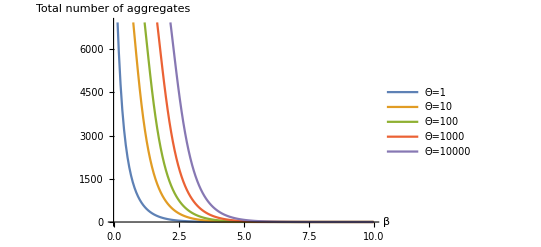

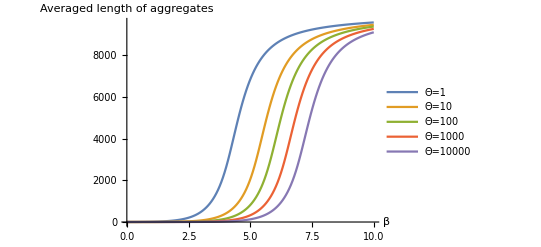

```mathematica
ListLinePlot[{(∑_(l=1)^10000 l^1.5×ⅇ^(-A05×l))/(∑_(l=1)^10000 l^2.5×ⅇ^(-A05×l))×10000,(∑_(l=1)^10000 l^1.5×ⅇ^(-A1×l))/(∑_(l=1)^10000 l^2.5×ⅇ^(-A1×l))×10000,(∑_(l=1)^10000 l^1.5×ⅇ^(-A105×l))/(∑_(l=1)^10000 l^2.5×ⅇ^(-A105×l))×10000,(∑_(l=1)^10000 l^1.5×ⅇ^(-A2×l))/(∑_(l=1)^10000 l^2.5×ⅇ^(-A2×l))×10000,(∑_(l=1)^10000 l^1.5×ⅇ^(-A205×l))/(∑_(l=1)^10000 l^2.5×ⅇ^(-A205×l))×10000},DataRange->{0,10},PlotLegends->{"Θ=1","Θ=10","Θ=100","Θ=1000","Θ=10000"},AxesLabel->{"β","Total number of aggregates"}]

ListLinePlot[{(∑_(l=1)^10000 l^2.5×ⅇ^(-A05×l))/(∑_(l=1)^10000 l^1.5×ⅇ^(-A05×l)),(∑_(l=1)^10000 l^2.5×ⅇ^(-A1×l))/(∑_(l=1)^10000 l^1.5×ⅇ^(-A1×l)),(∑_(l=1)^10000 l^2.5×ⅇ^(-A105×l))/(∑_(l=1)^10000 l^1.5×ⅇ^(-A105×l)),(∑_(l=1)^10000 l^2.5×ⅇ^(-A2×l))/(∑_(l=1)^10000 l^1.5×ⅇ^(-A2×l)),(∑_(l=1)^10000 l^2.5×ⅇ^(-A205×l))/(∑_(l=1)^10000 l^1.5×ⅇ^(-A205×l))},DataRange->{0,10},PlotLegends->{"Θ=1","Θ=10","Θ=100","Θ=1000","Θ=10000"},AxesLabel->{"β","Averaged length of aggregates"}]
```